# fraction overlap

## 2 dimensions

area of overlap as function of distance from optimum (d) and angle between optima (θ) [this uses the fact that the distance between the circle centres, x, is determined by d and θ in our case]

```mathematica
A[d_,θ_]:=2 d^2 ArcCos[x/(2d)]-x/2  √(4 d^2-x^2)/.x->d √(2(1-Cos[θ]))
```

overlap declines with angle (here from 0 to 180 degrees) for any distance

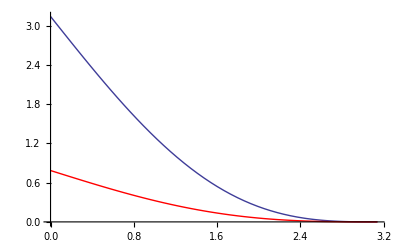

```mathematica
Show[
Plot[A[d,θ]/.d->1,{θ,0,π}],
Plot[A[d,θ]/.d->0.5,{θ,0,π},PlotStyle->Red],
PlotRange->All
]
```

overlap increases with distance for any angle

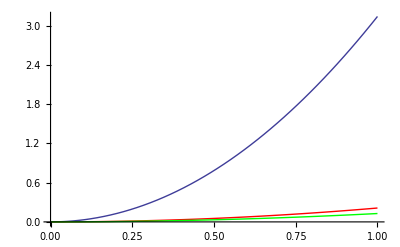

```mathematica
Show[
Plot[A[d,θ]/.θ->0,{d,0,1}],
Plot[A[d,θ]/.θ->90,{d,0,1},PlotStyle->Red],
Plot[A[d,θ]/.θ->180,{d,0,1},PlotStyle->Green],
PlotRange->All
]
```

but note that the fraction overlap is independent of the distance, d:

```mathematica
fA=Simplify[A[d,θ]/A[d,0],d>0]
```

(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π

and declines from 1 to 0 with angle

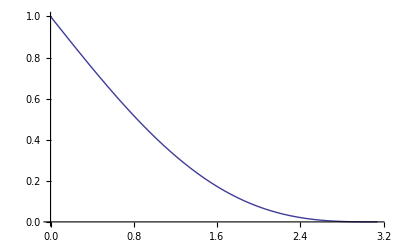

```mathematica
Show[
Plot[A[d,θ]/A[d,0]/.d->1,{θ,0,π}],
PlotRange->All
]
```

the fraction overlap is 0 when the angle is 180 degrees

```mathematica
A[d,θ]/A[d,0]/.θ->π
```

0

there is perfect overlap when the angle is 0

```mathematica
A[d,θ]/A[d,0]/.θ->0
```

1

distance and fraction overlap as functions of angle

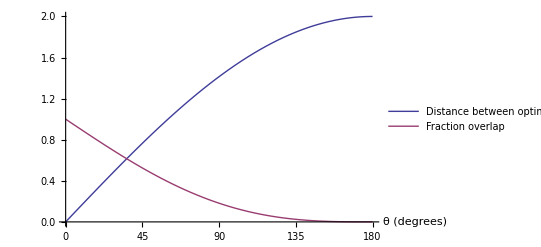

```mathematica
Plot[
{
d*√(2(1-Cos[θ*π/180]))/.d->1,
A[d,θ*π/180]/A[d,0]/.d->1
},
{θ,0,180},
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"θ (degrees)"},
PlotLegends->{"Distance between optima","Fraction overlap"}
]
```

fraction overlap as function of distance from optimum (d) and distance between circle centres (x) [together these determine the angle between optima]

```mathematica
A[x_,d_]:=2 d^2 ArcCos[x/(2d)]-x/2  √(4 d^2-x^2)
```

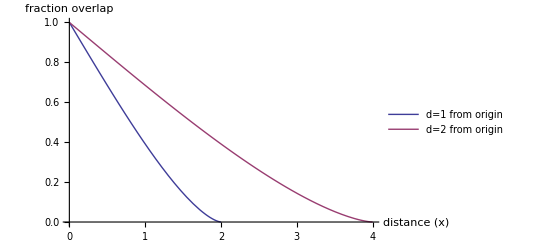

```mathematica
Plot[{A[x,d]/A[0,d]/.d->1,A[x,d]/A[0,d]/.d->2},{x,0,4},AxesLabel->{"distance (x)","fraction overlap"},
PlotLegends->{"d=1 from origin","d=2 from origin"}]
```

## 3 dimensions

http://mathworld.wolfram.com/Sphere-SphereIntersection.html

volume overlap bw spheres of radii r and R, with distance d between the centres

```mathematica
(π (R+r-d)^2(d^2+2d r-3 r^2+2d R+6r R-3 R^2))/(12d);
```

when both have same radii

```mathematica
%/.R->r//Simplify
```

1/12 π (d-2 r)^2 (d+4 r)

and when the distance between them is determined by the distance from the origin (also r) and the angle between them

```mathematica
V[r_,θ_]:=1/12 π (d-2 r)^2 (d+4 r)/.d->r √(2(1-Cos[θ]))
```

then the fraction overlap is

```mathematica
fV=V[r,θ]/V[r,0]//Simplify
```

1/16 (-2+√(2-2 Cos[θ]))^2 (4+√(2-2 Cos[θ]))

which is independent of the distance to the optimum, r, and declines with angle

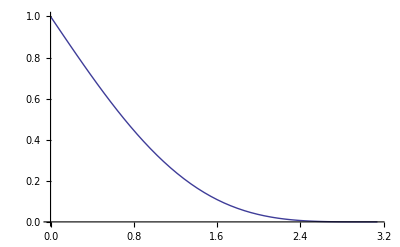

```mathematica
Plot[fV,{θ,0,π}]
```

Comparing to the 2 dimensional case

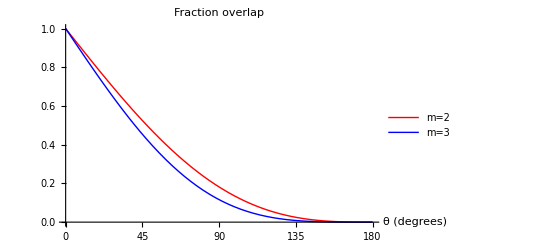

```mathematica
Plot[{fA/.θ->deg*π/180,fV/.θ->deg*π/180},{deg,0,180},PlotStyle->{{Red},{Blue}},
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"θ (degrees)"},
PlotLegends->{"m=2","m=3"},
PlotLabel->"Fraction overlap"
]
```

we see that the volume overlap (m=3) decreases even faster than the area overlap

## m dimensions

```mathematica
Clear[c1,c2,V]
```

Here we are interested in the volume of the intersection between two m-dimensional spheres, with centres at distance d, with radii r1 and r2. We follow Matt’s answer at https://math.stackexchange.com/questions/162250/how-to-compute-the-volume-of-intersection-between-two-hyperspheres

The volume of the intersection is the volume of two spherical caps, glued at a hyperplane.

The heights of the cap bases are

```mathematica
c1[d_,r1_,r2_]:=(d^2+r1^2-r2^2)/(2d)
```

```mathematica
c2[d_,r1_,r2_]:=(d^2-r1^2+r2^2)/(2d)
```

Computing the volume of these caps requires some fancy integration ( Concise Formulas for the Area and Volume of a Hyperspherical Cap, Shengqiao Li, Asian Journal of Mathematics and Statistics 4(1), 66-70, 2011). Turns out the volume of a cap is

```mathematica
V[m_,r_,a_]:=If[a≥0,1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2],π^(m/2)/Gamma[m/2+1] r^m-1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2]]
```

where a is the height of the cap base.

Thus the volume of the intersection is

```mathematica
Vint=V[m,r1,c1[d,r1,r2]]+V[m,r2,c2[d,r1,r2]];
```

and in our case we want both spheres to have the same radii, and the distance to depend on that radius and the angle between them (which we can restrict between 0 and 180 because 180 to 360 is just the same thing)

```mathematica
VintUs=Simplify[Vint/.r1->r/.r2->r/.d->r √(2(1-Cos[θ])),{r>0,m>0,0≤θ≤π}]
```

(π^(m/2) r^m BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2])/Gamma[1+m/2]

It looks like things are working (check areas/volumes of circle/sphere)

```mathematica
VintUs/.θ->0/.m->{2,3}
```

{π r^2,(4 π r^3)/3}

and no overlap if angle is 180deg

```mathematica
Simplify[VintUs/.θ->π,{r>0,m>0}]
```

0

Then the fraction overlap is

```mathematica
Vfraction=VintUs/(VintUs/.θ->0)
```

BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2]/BetaRegularized[1,(1+m)/2,1/2]

which is independent of r

Compare with previous results (m=2,3) to ensure consistent

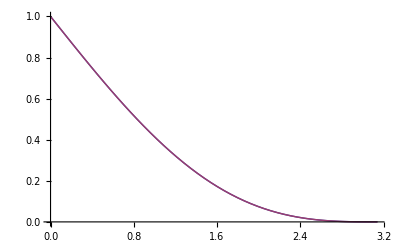

```mathematica
Plot[{Vfraction/.m->2,(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π},{θ,0,π}]
```

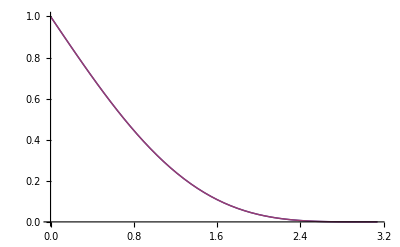

```mathematica
Plot[{Vfraction/.m->3,1/16 (-2+√(2-2 Cos[θ]))^2 (4+√(2-2 Cos[θ]))},{θ,0,π}]
```

And now we can clearly see the effect of dimensionality

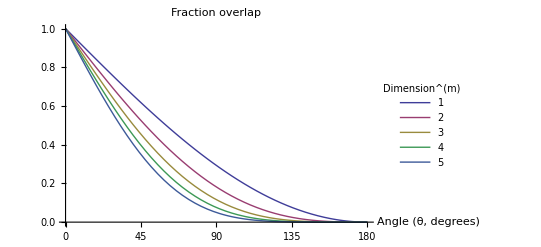

```mathematica
nms=5;
Plot[Evaluate@Table[Vfraction/.θ->θ π/180,{m,1,nms}],
{θ,0,180},
PlotLegends->Placed[LineLegend[Table[m,{m,1,nms}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"Angle (θ, degrees)"},
PlotLabel->"Fraction overlap"]
```

Solve for angle as a function of distance between hypersphere centres

```mathematica
Solve[x==d √(2(1-Cos[θ])),θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[(2 d^2-x^2)/(2 d^2)]},{θ→ArcCos[(2 d^2-x^2)/(2 d^2)]}}

and plot fraction overlap as function of distance between optima

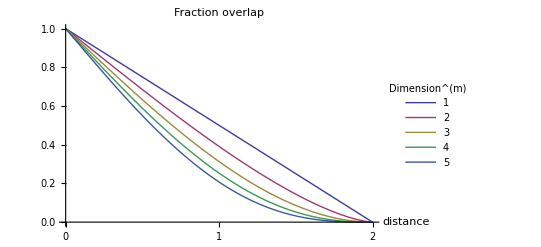

```mathematica
nms=5;
Plot[Evaluate@Table[Vfraction/.θ->ArcCos[(2 d^2-x^2)/(2 d^2)]/.d->1,{m,1,nms}],
{x,0,2},
PlotLegends->Placed[LineLegend[Table[m,{m,1,nms}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,1,2},Automatic},
AxesLabel->{"distance"},
PlotLabel->"Fraction overlap"]
```